## MergeVertices-example.nb

Example Cellzilla2D notebook

GPL License applies.
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51e (11 June 2017)) loaded Sun 11 Jun 2017 10:35:59
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

## Define a tissue

```mathematica
T=Tissue[{{2.029964791566701,9.432895587599681},{3.378819336150339,2.620588165527875},{3.8989778700460884,2.201869824673844},{4.782118830588536,0.8451726289903713},{6.0606911288404985,5.098725501972692},{7.397332498858528,4.603254692381817},{7.671976649800004,4.34534187735987},{7.812099951289529,7.897362417079099},{8.4679327514499,4.1155370096908},{9.081223779179746,3.7162488016436965},{9.295692967853698,7.363626544649637},{10.764364327712675,5.1687562764223065},{13.071738739807987,3.0059000237502262},{15,4},{11,9},{-1,10},{0,0},{10,0},{12.619674838828677,6.975406451464151},{12.090335075481628,7.637081155647965},{12.05662752555679,7.679215593054014},{6.370188470306949,9.38581762747442},{1.863986255478454,9.761334478710129},{-0.21290021085814465,2.1290021085814463},{4.992637801352049,0.},{10.363352319467635,0.29068185557410775},{13.238788833309988,2.59103106664799}},{{1,2},{1,5},{1,23},{2,3},{2,24},{3,4},{3,5},{4,7},{4,25},{5,6},{6,7},{6,8},{7,9},{8,11},{8,22},{9,10},{9,11},{10,12},{10,26},{11,21},{12,13},{12,20},{13,19},{13,27},{14,19},{14,27},{15,21},{15,22},{16,23},{16,24},{17,24},{17,25},{18,25},{18,26},{19,20},{20,21},{22,23},{26,27}},{{4,7,2,1},{28,15,14,20,27},{35,22,21,23},{34,19,16,13,8,9,33},{38,24,21,18,19},{37,3,2,10,12,15},{23,24,26,25},{30,5,1,3,29},{6,8,11,10,7},{36,20,17,16,18,22},{11,13,17,14,12},{32,9,6,4,5,31}}];
```

## Merge two vertices by referencing the vertex number

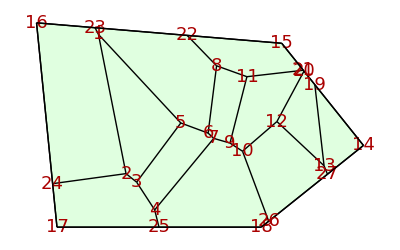

```mathematica
ShowTissue[T, "VertexNumbers"-> True, "VertexNumberStyle"-> 18]
```

```mathematica
T1=MergeVertices[T,{15,22}];
```

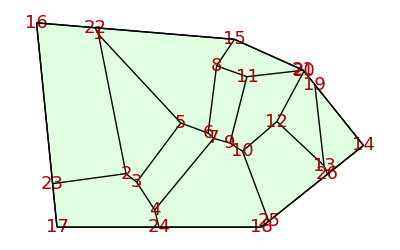

```mathematica
ShowTissue[T1, "VertexNumbers"-> True, "VertexNumberStyle"-> 18]
```

## Merge two vertices by referencing an edge between them

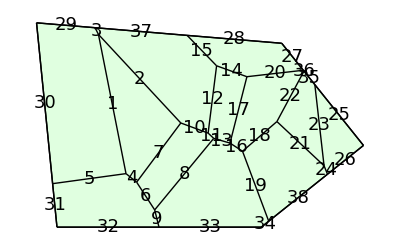

```mathematica
ShowTissue[T,  "EdgeNumberStyle"-> 18, "EdgeNumbers"-> True]
```

```mathematica
T2=MergeVertices[T,31];
```

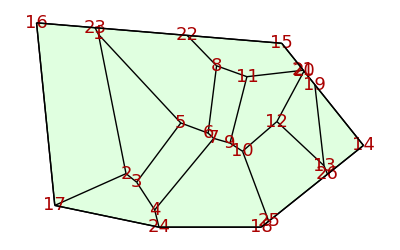

```mathematica
ShowTissue[T2, "VertexNumbers"-> True, "VertexNumberStyle"-> 18]
```